```mathematica
ClearAll[bddGraph];
bddGraph[bf_]:=With[{eq=Replace[BooleanConvert[bf,"IF"],If->List,∞,Heads->True]},Graph[(Labeled[#,Extract[eq,#~Append~1]]&/@Position[eq,_List])~Join~(Labeled[#,#]&/@{True,False}),Flatten[{Labeled[#->#~Append~2,True],Labeled[#->#~Append~3,False]}&/@Position[eq,_List],2]/.a_->b_:>a->Extract[eq,b]/;BooleanQ[Extract[eq,b]]]]
```

!(16⊻z⇒7.15599||9)⇒16&&9

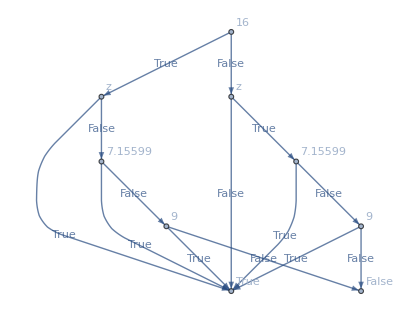

```mathematica
bf=Implies[Not[Implies[Xor[z,x],Or[t,y]]],And[x,y]]
bddGraph[bf]
```

16&&9

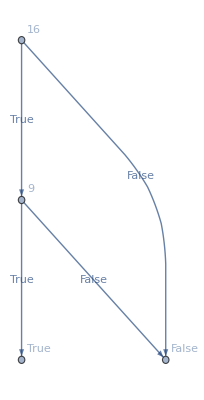

```mathematica
bf=And[x,y]
bddGraph[bf]
```

16⊽(9⇒z)

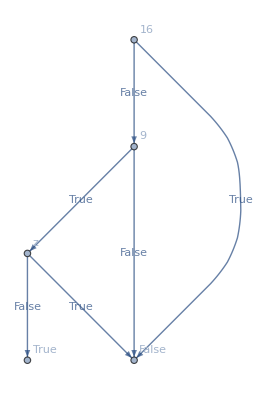

```mathematica
bf=Nor[x,Implies[y,z]]
bddGraph[bf]
```

(7.15599⧦!16)⊻(16⊽(9⇒z))

!(16⊻z⇒7.15599||9)⇒16&&9

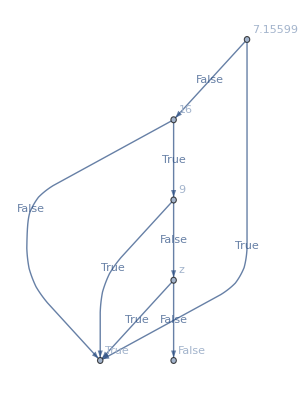

```mathematica
f1=Xor[Nor[x,Implies[y,z]],Equivalent[t,!x]]
f2=Implies[Not[Implies[Xor[z,x],Or[t,y]]],And[x,y]]
bddGraph[Implies[f1,f2]]
```